## Without Disorder

{101,2}

FindFormula = 0.999462-0.0000392706 t

Mean P(x=0) = 0.9974983366

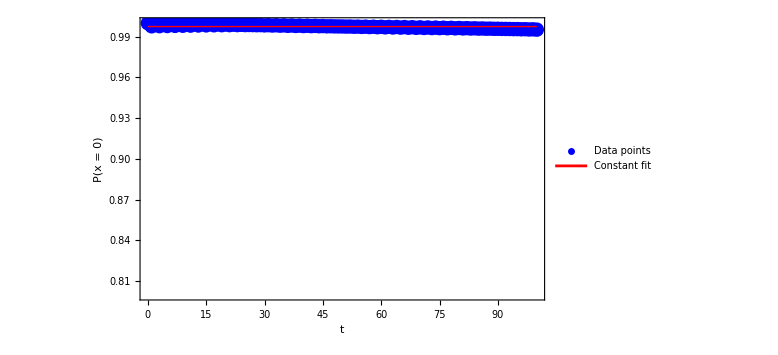

RMSE = 0.001218023239

Standard deviation = 0.001224098206

Maximum absolute residual = 0.0025016634

```mathematica
SetDirectory["C:\\Users\\MINI\\Downloads"];

pro=Import["withoutdisorder.dat","Table"];
Dimensions[pro]

tmax=100;

tVals=pro[[1;;tmax+1,1]];
Px0=pro[[1;;tmax+1,2]];

data=Transpose[{tVals,Px0}];


formula=FindFormula[data,t];

Print["FindFormula = ",formula];

constt=Mean[Px0];

Print["Mean P(x=0) = ",N[constt,10]];

Show[{ListPlot[data,PlotStyle->{Blue,PointSize[0.018]},PlotLegends->Placed[{Style["Data points",16,Bold]},{0.80,0.20}]],Plot[constt,{t,0,tmax},PlotStyle->{Red,Thick},PlotLegends->Placed[{Style["Constant fit",16,Bold]},{0.80,0.30}]]},Frame->True,FrameLabel->{Style["t",20,Bold],Style["P(x = 0)",20,Bold]},FrameTicksStyle->Directive[14,Bold],FrameStyle->Thick,PlotRange->{{0,tmax},{0.8,1.0}},ImageSize->Large]
res=Px0-constt;

rmse=N[Sqrt[Mean[res^2]],10];

Print["RMSE = ",rmse];


std=N[StandardDeviation[Px0],10];

Print["Standard deviation = ",std];

maxres=N[Max[Abs[res]],10];

Print["Maximum absolute residual = ",maxres];
```

## Stat-Small

{101,2}

0.999812-0.0000865105 t

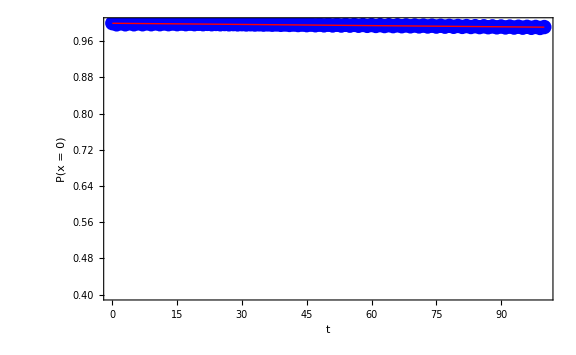

0.000929033 Error

```mathematica
SetDirectory["C:\\Users\\MINI\\Downloads"];
(*Import data*)
pro=Import["stat001.dat","Table"];
Dimensions[pro]

Px0=pro[[All,2]];(*first column=x=0*)
tVals=pro[[All,1]];
data=Transpose[{tVals,Px0}];
formula=FindFormula[data,t]

(*Plot original vs fit*)
Show[{ListPlot[data,PlotStyle->{Blue,PointSize[0.018]},PlotRange->{{0,100},{0.4,1}},PlotLegends->Placed[{Style["Data points",16,Bold]},{0.7,0.4}]],Plot[formula,{t,0,100},PlotStyle->{Red,Thick},PlotRange->{{0,100},{0.4,1}},PlotLegends->Placed[{Style["Fit (Very slow decay)",16,Bold]},{0.7,0.4}]]},Frame->True,FrameLabel->{Style["t",18,Bold],Style["P(x = 0)",18,Bold]},FrameTicksStyle->Directive[14,Bold],FrameStyle->Thick,ImageSize->Large]

(*Compute residuals*)
f=FindFormula[data,t];
res=Px0-(f/.t->tVals);
(*Compute RMSE and plot residuals*)
N[Sqrt[Mean[res^2]]] "Error"
ListPlot[res,Frame->True,FrameLabel->{"Index","Residual"},PlotStyle->Blue];
```

## Stat-Large

{101,2}

0.999853-0.000195174 t

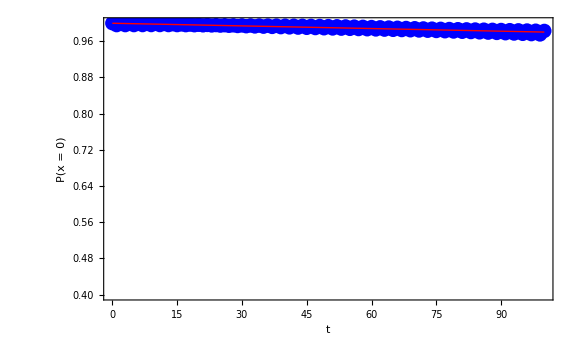

0.00244376 Error

```mathematica
SetDirectory["C:\\Users\\MINI\\Downloads"];
(*Import data*)
pro=Import["stat002.dat","Table"];
Dimensions[pro]

Px0=pro[[All,2]];(*first column=x=0*)
tVals=pro[[All,1]];
data=Transpose[{tVals,Px0}];
formula=FindFormula[data,t]

(*Plot original vs fit*)
Show[{ListPlot[data,PlotStyle->{Blue,PointSize[0.018]},PlotRange->{{0,100},{0.4,1}},PlotLegends->Placed[{Style["Data points",16,Bold]},{0.7,0.4}]],Plot[formula,{t,0,100},PlotStyle->{Red,Thick},PlotRange->{{0,100},{0.4,1}},PlotLegends->Placed[{Style["Fit (Very slow decay)",16,Bold]},{0.7,0.4}]]},Frame->True,FrameLabel->{Style["t",18,Bold],Style["P(x = 0)",18,Bold]},FrameTicksStyle->Directive[14,Bold],FrameStyle->Thick,ImageSize->Large]

(*Compute residuals*)
f=FindFormula[data,t];
res=Px0-(f/.t->tVals);
(*Compute RMSE and plot residuals*)
N[Sqrt[Mean[res^2]]] "Error"
ListPlot[res,Frame->True,FrameLabel->{"Index","Residual"},PlotStyle->Blue];
```

## Dyn-small

{101,7}

Piecewise[{{0.999197-0.000421256 t, 0≤t<20.2861}, {1.04069-0.0000279808 t-0.0167924 Log[t], 20.2861≤t<68.262}, {0.985265-0.000224042 t, 68.262≤t<100.}, {0, True}}]

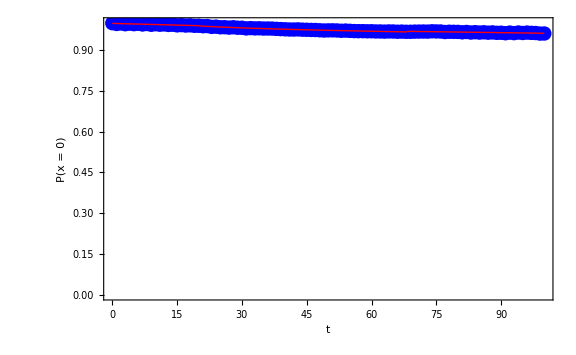

```mathematica
SetDirectory["C:\\Users\\MINI\\Downloads"];
(*Import data*)
pro=Import["dyn001_50.dat","Table"];
Dimensions[pro]

Px0=pro[[All,1]];(*first column=x=0*)
tVals=Range[0,Length[Px0]-1];
data=Transpose[{tVals,Px0}];
formula=FindFormula[data,t]

(*Plot original vs fit*)
Show[{ListPlot[data,PlotStyle->{Blue,PointSize[0.018]},PlotRange->{{0,100},{0.0,1}},PlotLegends->Placed[{Style["Data points",16,Bold]},{0.7,0.4}]],Plot[formula,{t,0,100},PlotStyle->{Red,Thick},PlotRange->{{0,100},{0.0,1}},PlotLegends->Placed[{Style["Fit (Slow decay)",16,Bold]},{0.7,0.4}]]},Frame->True,FrameLabel->{Style["t",18,Bold],Style["P(x = 0)",18,Bold]},FrameTicksStyle->Directive[14,Bold],FrameStyle->Thick,ImageSize->Large]

(*Compute residuals*)
f=FindFormula[data,t];
res=Px0-(f/.t->tVals);
(*Compute RMSE and plot residuals*)
N[Sqrt[Mean[res^2]]] "Error"
ListPlot[res,Frame->True,FrameLabel->{"Index","Residual"},PlotStyle->Blue];
```

{aa→1.00128,b→-0.000716971,c→3.63496×10^-6,d→-1.77871×10^-9}

0.00124813 RMSE

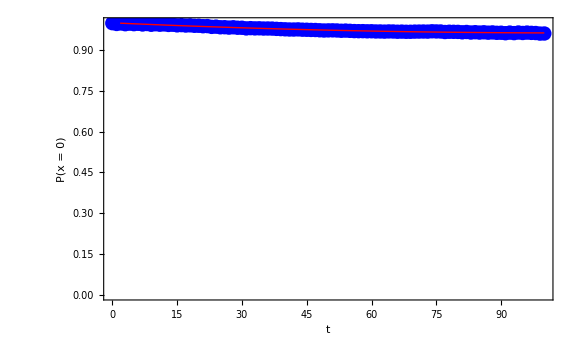

```mathematica
para=FindFit[data,aa+b*t+c*t^2+d*t^3,{aa,b,c,d},t] (*for small-stat disorder*)
aa=aa/.para;
b=b/.para;
c=c/.para;
d=d/.para;
Fitt=aa+b*t+c*t^2+d*t^3;
rmse=Sqrt[Mean[(data[[All,2]]-(Fitt/.t->data[[All,1]]))^2]] "RMSE"
Show[{ListPlot[data,PlotStyle->{Blue,PointSize[0.018]},PlotRange->{{0,100},{0.0,1}},PlotLegends->Placed[{Style["Data points",16,Bold]},{0.65,0.4}]],Plot[Fitt,{t,0,100},PlotStyle->{Red,Thick},PlotRange->{{0,100},{0.0,1}},PlotLegends->Placed[{Style["Fit (very slow decay)",16,Bold]},{0.65,0.4}]]},Frame->True,FrameLabel->{Style["t",18,Bold],Style["P(x = 0)",18,Bold]},FrameTicksStyle->Directive[14,Bold],FrameStyle->Thick,ImageSize->Large]
```

## Dyn-large

{101,7}

Piecewise[{{0.998983-0.00146136 t, 0≤t<28.3362}, {1.01597-0.001809 t, 28.3362≤t<50.}, {0.976177-0.000907852 t, 50.≤t<98.5179}, {0.00893197 t, 98.5179≤t<100.}, {0, True}}]

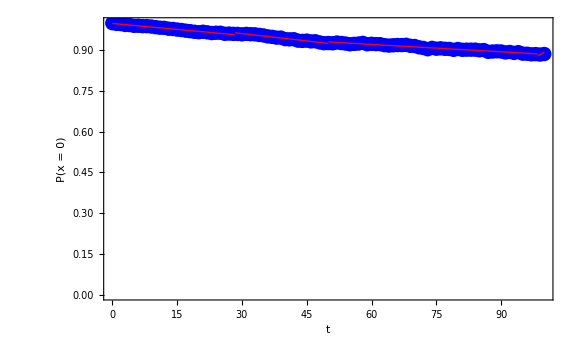

```mathematica
SetDirectory["C:\\Users\\MINI\\Downloads"];
(*Import data*)
pro=Import["dyn002_50.dat","Table"];
Dimensions[pro]

Px0=pro[[All,1]];(*first column=x=0*)
tVals=Range[0,Length[Px0]-1];
data=Transpose[{tVals,Px0}];
formula=FindFormula[data,t]

(*Plot original vs fit*)
Show[{ListPlot[data,PlotStyle->{Blue,PointSize[0.018]},PlotRange->{{0,100},{0.0,1}},PlotLegends->Placed[{Style["Data points",16,Bold]},{0.7,0.4}]],Plot[formula,{t,0,100},PlotStyle->{Red,Thick},PlotRange->{{0,100},{0.0,1}},PlotLegends->Placed[{Style["Fit (Slow decay)",16,Bold]},{0.7,0.4}]]},Frame->True,FrameLabel->{Style["t",18,Bold],Style["P(x = 0)",18,Bold]},FrameTicksStyle->Directive[14,Bold],FrameStyle->Thick,ImageSize->Large]

(*Compute residuals*)
f=FindFormula[data,t];
res=Px0-(f/.t->tVals);
(*Compute RMSE and plot residuals*)
N[Sqrt[Mean[res^2]]] "Error"
ListPlot[res,Frame->True,FrameLabel->{"Index","Residual"},PlotStyle->Blue];
```

{aa→1.00035,b→-0.00167914,c→7.5494×10^-6,d→-2.22562×10^-8}

0.0027548 RMSE

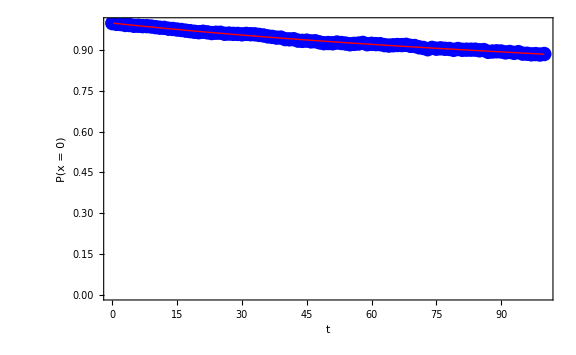

```mathematica
para=FindFit[data,aa+b*t+c*t^2+d*t^3,{aa,b,c,d},t] 
aa=aa/.para;
b=b/.para;
c=c/.para;
d=d/.para;
Fitt=aa+b*t+c*t^2+d*t^3;
rmse=Sqrt[Mean[(data[[All,2]]-(Fitt/.t->data[[All,1]]))^2]] "RMSE"
Show[{ListPlot[data,PlotStyle->{Blue,PointSize[0.018]},PlotRange->{{0,100},{0.0,1}},PlotLegends->Placed[{Style["Data points",16,Bold]},{0.65,0.4}]],Plot[Fitt,{t,0,100},PlotStyle->{Red,Thick},PlotRange->{{0,100},{0.0,1}},PlotLegends->Placed[{Style["Fit (Slow decay)",16,Bold]},{0.65,0.4}]]},Frame->True,FrameLabel->{Style["t",18,Bold],Style["P(x = 0)",18,Bold]},FrameTicksStyle->Directive[14,Bold],FrameStyle->Thick,ImageSize->Large]
```

## Phase-large

Phase-B

{101,2}

1.00389-0.000493975 t

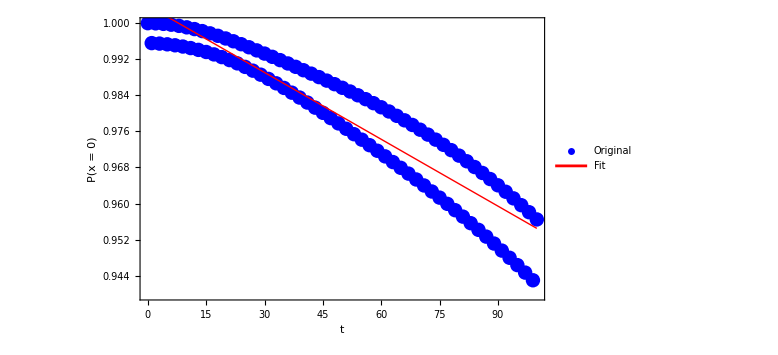

{aa→0.998515,b→-0.000129847,c→-4.77708×10^-6,d→1.25783×10^-8}

0.00471334 RMSE

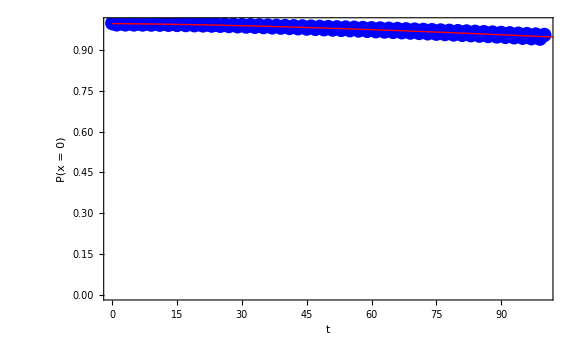

```mathematica
"Phase-B"
SetDirectory["C:\\Users\\MINI\\Downloads"];
(*Import data*)
pro=Import["C:\\Users\\MINI\\Downloads\\phasepreserving_8c_New.dat","Table"];
Dimensions[pro]

Px0=pro[[All,2]];(*first column=x=0*)tVals= pro[[All,1]];
data=Transpose[{tVals,Px0}];
formula=FindFormula[data,t]

(*Plot original vs fit*)
Show[{ListPlot[data,PlotStyle->{Blue,PointSize[0.018]},PlotLegends->Placed[{"Original"},{0.8,0.85}]],Plot[formula,{t,0,Max[tVals]},PlotStyle->{Red,Thick},PlotLegends->Placed[{"Fit"},{0.8,0.78}]]},Frame->True,FrameLabel->{Style["t",18,Bold],Style["P(x = 0)",18,Bold]},FrameTicksStyle->Directive[14,Bold],FrameStyle->Thick,ImageSize->Large]
(*Polynomial Fit*)
para=FindFit[data,aa+b*t+c*t^2+d*t^3,{aa,b,c,d},t] (*for Phase Pert*)
aa=aa/.para;
b=b/.para;
c=c/.para;
d=d/.para;
Fitt=aa+b*t+c*t^2+d*t^3;
rmse=Sqrt[Mean[(data[[All,2]]-(Fitt/.t->data[[All,1]]))^2]] "RMSE"

Show[{ListPlot[data,PlotStyle->{Blue,PointSize[0.018]},PlotLegends->Placed[{Style["Data points",16,Bold]},{0.65,0.5}]],Plot[Fitt,{t,0,300},PlotStyle->{Red,Thick},PlotLegends->Placed[{Style["Fit (slow decay)",16,Bold]},{0.65,0.5}]]},Frame->True,FrameLabel->{Style["t",18,Bold],Style["P(x = 0)",18,Bold]},FrameTicksStyle->Directive[14,Bold],FrameStyle->Thick,ImageSize->Large,PlotRange->{{0,100},{0,1}}]
```

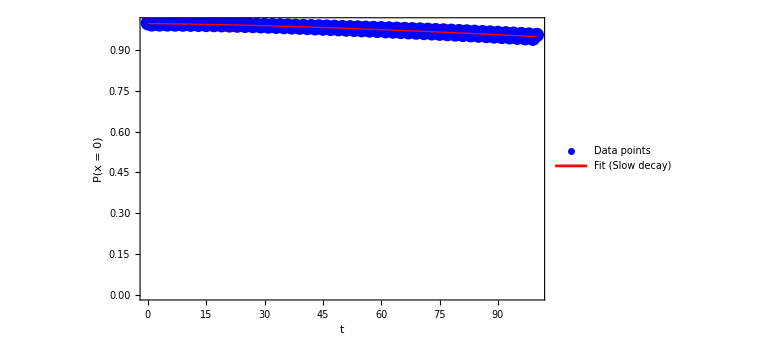

```mathematica
Show[{ListPlot[data,PlotStyle->{Blue,PointSize[0.018]},PlotLegends->Placed[{Style["Data points",16,Bold]},{0.78,0.88}],PlotRange->{{0,100},{0.0,1}},GridLines->None],Plot[Fitt,{t,0,100},PlotStyle->{Red,Thick},PlotLegends->Placed[{Style["Fit (Slow decay)",16,Bold]},{0.78,0.78}],PlotRange->{{0,100},{0.0,1}},GridLines->None]},Frame->True,FrameLabel->{Style["t",20,Bold],Style["P(x = 0)",20,Bold]},FrameTicksStyle->Directive[14,Bold],FrameStyle->Thick,PlotRange->{{0,100},{0.0,1}},GridLines->None,ImageSize->Large]
```

## Phase-Small

Phase-B

{101,2}

0.99988-0.0000891705 t

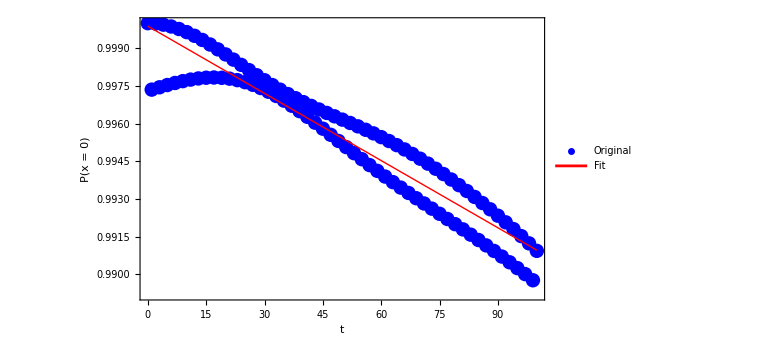

{aa→0.99897,b→-0.0000198379,c→-1.11586×10^-6,d→4.67931×10^-9}

0.00071614 RMSE

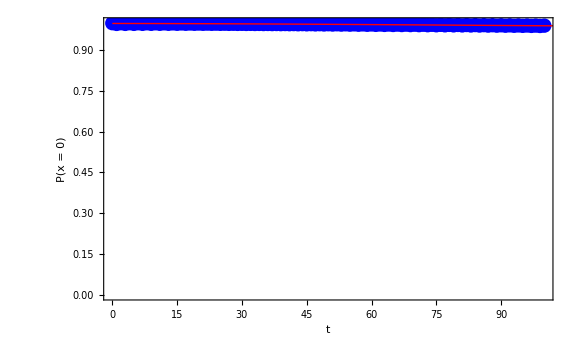

```mathematica
"Phase-B"
SetDirectory["C:\\Users\\MINI\\Downloads"];
(*Import data*)
pro=Import["C:\\Users\\MINI\\Downloads\\phasepreserving_8b.dat","Table"];
Dimensions[pro]

Px0=pro[[All,2]];(*first column=x=0*)tVals= pro[[All,1]];
data=Transpose[{tVals,Px0}];
formula=FindFormula[data,t]

(*Plot original vs fit*)
Show[{ListPlot[data,PlotStyle->{Blue,PointSize[0.018]},PlotLegends->Placed[{"Original"},{0.8,0.85}]],Plot[formula,{t,0,Max[tVals]},PlotStyle->{Red,Thick},PlotLegends->Placed[{"Fit"},{0.8,0.78}]]},Frame->True,FrameLabel->{Style["t",18,Bold],Style["P(x = 0)",18,Bold]},FrameTicksStyle->Directive[14,Bold],FrameStyle->Thick,ImageSize->Large]
(*Polynomial Fit*)
para=FindFit[data,aa+b*t+c*t^2+d*t^3,{aa,b,c,d},t] (*for Phase Pert*)
aa=aa/.para;
b=b/.para;
c=c/.para;
d=d/.para;
Fitt=aa+b*t+c*t^2+d*t^3;
rmse=Sqrt[Mean[(data[[All,2]]-(Fitt/.t->data[[All,1]]))^2]] "RMSE"

Show[{ListPlot[data,PlotStyle->{Blue,PointSize[0.018]},PlotLegends->Placed[{Style["Data points",16,Bold]},{0.65,0.5}]],Plot[Fitt,{t,0,300},PlotStyle->{Red,Thick},PlotLegends->Placed[{Style["Fit (very slow decay)",16,Bold]},{0.65,0.5}]]},Frame->True,FrameLabel->{Style["t",18,Bold],Style["P(x = 0)",18,Bold]},FrameTicksStyle->Directive[14,Bold],FrameStyle->Thick,ImageSize->Large,PlotRange->{{0,100},{0,1}}]
```